```mathematica
Log10[1]
```

## Exclusion Plots, Run ~/Dropbox/nEDM/NStar/mNStar/mBpSens_2012.nb

## Initialize

```mathematica
OS="win";(*or,linux*)
(*SetOptions[$FrontEndSession,NotebookAutoSave->True]*)
NotebookSave[]
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c_old.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]]
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};

(***)
Print["oILL {Volume (m^3), Surface Area (m^2) = { ", voloill=Pi*(.24)^2*.12," , ",saoill=(2*Pi*(.24)^2)+(2Pi*.12*.24)," } "];
Print["NStar {Volume (m^3), Surface Area (m^2) = { ", voloill=Pi*(.24)^2*.12," , ",saoill=(2*Pi*(.24)^2)+(2Pi*.12*.24)," } "];
oillr=.24;oillh=.12;
Print["oILL {Volume (m^3), Surface Area (m^2) = { ", voloill=Pi*(oillr)^2*oillh," , ",saoill=(2*Pi*(oillr)^2)+(2Pi*oillr*oillh)," } "];
newr=1.4;newh=3.5;
Print["Diameter (1.14m) < ", N[Sqrt[(2newr)^2+newh^2]]];
Print["NStar_Capsule {Volume (m^3), Surface Area (m^2) = { ", volnew=N[10Pi newr^2/3]," , ",sanew=N[8Pi*newr^2]," } "];
Print["4V/A {oILL, NStar} (m) = { ",4voloill/saoill," , ",4volnew/sanew," } "];
(***)
taue[bp_,bb_,m_]:=√(bb^2/(2 bp^2)(3 bp^2-bb^2)/((bb^2-bp^2)^2))    
taubca[bp_,bb_,m_]:=√((bp bb)/((bb^2-bp^2)^2)) 
taubr[bp_,bb_,m_]:=m √(bp/(bb(bb^2-bp^2))) ;
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

36

oILL {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

NStar {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

oILL {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

Diameter (1.14m) < 4.48219

NStar_Capsule {Volume (m^3), Surface Area (m^2) = { 20.5251 , 49.2602 }

4V/A {oILL, NStar} (m) = { 0.16 , 1.66667 }

```mathematica
(*If we wanted to compare sensitivity increase by enlarging the volume of storage: Not used here*)
```

oILL {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

NStar {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

oILL {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

Diameter (1.14m) < 4.48219

NStar_Capsule {Volume (m^3), Surface Area (m^2) = { 20.5251 , 49.2602 }

4V/A {oILL, NStar} (m) = { 0.16 , 1.66667 }

## Read ZB’s list

```mathematica
zbdata=ReadList[StringJoin[descDir,seperator,"Lista_zb.dat"],{Real,Real,Real,Real,Real,Real}];
dimzbdata=Dimensions[zbdata][[1]];
ptzba=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[2]]},{k,1,dimzbdata}];
fzba=Interpolation[ptzba];(*A*)
ptzbe=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[3]]},{k,1,dimzbdata}];
fzbe=Interpolation[ptzbe];(*E*)
ptzbsignal1=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[4]]},{k,1,dimzbdata}];
fzbsignal1=Interpolation[ptzbsignal1];(*A*)
ptzbsignal2=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[5]]},{k,1,dimzbdata}];
fzbsignal2=Interpolation[ptzbsignal2];(*A*)
ptzbsignal3=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[6]]*2.56/1.96},{k,1,dimzbdata}];
fzbsignal3=Interpolation[ptzbsignal3];(*E*)
```

```mathematica
(*ω (<t_f>-1.96Sigma) < 1 *)
tf1=0.0739093+1.96*0.00401555
ω=2Pi/tf1;
γ=1.8*10^2; (*in Hz/μΤ*)
Print["B < ",bp=ω/(γ)]
Print["B (95% C.L.) < ",bp/1.96]
```

0.0817798

B < 0.426836

B (95% C.L.) < 0.217774

```mathematica
(*ω' (<t_f>-1.96Sigma) > 1 *)
tf2=(*0.0610227-1.96*0.00336746*)0.0502391-1.96*0.00239672
ω=2Pi/tf2;
γ=1.8*10^2; (*in Hz/μΤ*)
Print["B' > ",bp=ω/(γ)]
Print["B' (95% C.L.) > ",bp*1.96]
```

0.0455415

B' > 0.766478

B' (95% C.L.) > 1.5023

```mathematica
(*For Ramsey type measurement*)
wup=PlusMinus[3.8424583,0.0000026]
wdown=PlusMinus[ 3.8424562,0.0000030]
asym=2(wup-wdown)/(wup+wdown)
```

3.84246±2.6×10^-6

3.84246±3.×10^-6

5.×10^-7±1.×10^-6

## Separate Plots

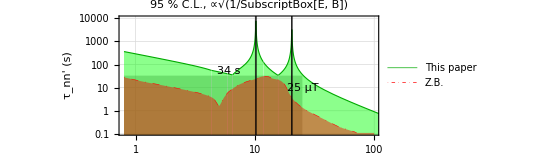

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\fin_sens1-e_s2.png

```mathematica
(*These create appropriate integers*)
tk3[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,SetPrecision[10^j,3],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[2*int]],u,int}]
],3];
tk32[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,SetPrecision[10^j,3],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[2*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[3*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[4*int]],u,int}]~Join~
Table[{10^j,"",{N[c],d}},{j,l+N[Log10[5*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[6*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[7*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[8*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[9*int]],u,int}]
],3];
(*Only marked lines are data lines, rest are for making regions from other papers*)
thk=.001;
exprt2=LogLogPlot[
{
(*1*)ConditionalExpression[33,0<bp<25],

(*13*)(taue[bp*10^(-6),Mean[b10][[1]],me1095]),(taue[bp*10^(-6),Mean[b20][[1]],me2095]),(*Actual limit: E, plotting 10, 20 muT separately*)

(*16*)ConditionalExpression[fzbe[bp],0.5<bp<100]
},{bp,.8,3000},
PlotRange->{{.126,99},{.11,9999}},Axes->None,GridLines->Automatic,
Filling->{{1->{0.001,Directive[Opacity[.45],Gray]}},{(*13*)2->{0.001,Directive[Opacity[.45],Green]}},{3(*16*)->{0.001,Directive[Opacity[.45],Red]}}},
PlotStyle->{(*1*)None,(*13*){Automatic,Thickness[thk],Darker[Green]},(*16*){DotDashed,Thickness[thk/2],Red}},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-1,4,.02,0,0.015,0,1],tk22[-1,4,.02,0,0.015,0,1]},{tk3[-1,3,.02,0,0.015,0,1/4],tk22[-1,3,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn' (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
PlotLegends->Placed[LineLegend[Flatten[Join[Table["",{k,1,1}],{"This paper","Z.B."}]],LegendLayout->{"Row",1}],Bottom],
PlotLabel->"95 % C.L., ∝√(1/SubscriptBox[E, B])",
Epilog->{
{Directive[{PointSize[.0075],Black}](*,pnt3,pnt4,pnt5*)},
{Directive[lineStyle],ln1,ln2,
Text[Style["34 s",FontSize->Large],Log@{6,50}],
Text[Style["25 μT",FontSize->Large],Log@{25,10}],
(*Text[Style["7.8 s",FontSize->Large],Log@{1,5}],
Text[Style["15 μT",FontSize->Large],Log@{8,.1}],
Text[Style["28 μT",FontSize->Large],Log@{32,.1}]*)}
},ImageSize->{1400},AspectRatio->1/2.5
]
Export[StringJoin[PicDir,seperator,"fin_sens1-e_s2.png"],exprt2]
```

```mathematica
(*Only marked lines are data lines, rest are for making regions from other papers*)
```

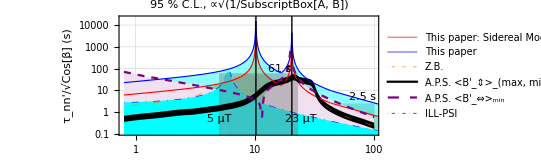

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\fin_sens1-a_s2.png

```mathematica
exprt3=LogLogPlot[
{
(*1*)ConditionalExpression[2.5,.8<bp<100],
(*14*)(taubca[bp*10^(-6),Mean[b10][[1]],mac1095]),(taubca[bp*10^(-6),Mean[b20][[1]],mac2095]),(*Sidereal oscillation Limit*)
(*15*)(taubca[bp*10^(-6),Mean[b10][[1]],ma1095]),(taubca[bp*10^(-6),Mean[b20][[1]],ma2095]),(*Actual limit: A*)
(*17*)ConditionalExpression[fzba[bp],0.5<bp<100],
(**)
(*18*)ConditionalExpression[fzbsignal1[bp],0.5<bp<100],
(*19*)ConditionalExpression[fzbsignal2[bp],0.5<bp<100],
(*20*)ConditionalExpression[fzbsignal3[bp],0.5<bp<100],
(*21*)Sqrt[.32^2-(bp-6)^2]*100+40,
(*22*)ConditionalExpression[taubppnpi[6,bp,198,0,380,tfoill]/7,((bp<5.7)||(bp>6.3))],
(**)
(*23*)ConditionalExpression[61,5<bp<23]
},{bp,.8,3000},
PlotRange->{{.126,99},{.11,20499}},Axes->None,GridLines->Automatic,
Filling->{{1->{0.001,Directive[Opacity[.45],Gray]}},{(*15*)3->{0.001,Directive[Opacity[.45],Cyan]}},{(*14*)2->{0.001,Directive[Opacity[.45],Orange]}},{(*17*)4->{0.001,Automatic}},{(*18*)5->{{6(*19*)},Black}},{7(*20*)->{0.001,LightPurple}},{9(*22*)->{.01,Cyan}},{8(*21*)->{.01,Cyan}},{(*23*)10->{0.001,Directive[Opacity[.45],Gray]}}},
PlotStyle->{None,(*14*){Red,Thickness[thk]},(*15*){Blue,Thickness[thk]},(*17*){DotDashed,Thickness[thk/2],Orange},(*18*)Black,(*19*)None,(*20*){Dashed,Purple},(*21*){DotDashed,Thickness[thk/2],Blue},(*22*){DotDashed,Thickness[thk/2],Blue},(*23*)None},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-1,5,.02,0,0.015,0,1],tk22[-1,5,.02,0,0.015,0,1]},{tk3[-1,3,.02,0,0.015,0,1/4],tk22[-1,3,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn'/√Cos[β] (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
PlotLegends->Placed[LineLegend[Flatten[Join[Table["",{k,1,1}],{"This paper: Sidereal Modulation, Cos[β=Ωt]","This paper","Z.B.","A.P.S. <B'_⇕>_(max, min)","","A.P.S. <B'_⇔>_min","ILL-PSI"}]],LegendLayout->{"Row",2}],Bottom],
PlotLabel->"95 % C.L., ∝√(1/SubscriptBox[A, B])",
Epilog->{
{Directive[{PointSize[.0075],Black}]},
{Directive[lineStyle],ln1,ln2,
Text[Style["2.5 s",FontSize->Large],Log@{80,5}],
(*Text[Style["25 μT",FontSize->Large],Log@{25,10}],*)
Text[Style["61 s",FontSize->Large],Log@{16,100}],
Text[Style["5 μT",FontSize->Large],Log@{5,.5}],
Text[Style["23 μT",FontSize->Large],Log@{24,.5}]}
},ImageSize->{1400},AspectRatio->1/2.5
]
Export[StringJoin[PicDir,seperator,"fin_sens1-a_s2.png"],exprt3]
```